```mathematica
(* For Exporting *)
SetDirectory[NotebookDirectory[]];

bin=Databin["66W7CW2x"];

(* Take the arbitrary number stored and convert it to a DateObject, then a string *)
times=DateObject/@Dataset[bin][All,"Timestamp"]//Normal;

(* Place all data in chronological order *)
chronologicalOrdering=Ordering[times];
latestIndex=chronologicalOrdering[[Length[times]]];
gopDebates=DateObject/@{"August 6, 2015 8pm","September 16, 2015 7pm"};
(* Use the names from the last row to be sure to have them all *)
names=Select[Keys[Dataset[bin][latestIndex]]//Normal,StringContainsQ[#,"("]&];
Clear[data];

times=times[[chronologicalOrdering]];
data=names/.(Dataset[bin][chronologicalOrdering,names]//Normal);

(* At this point, all data is in chronological order *)
times=DateString/@times;

dayTimes=N[(AbsoluteTime[#]-AbsoluteTime[times[[Length[times]]]])/(3600*24)]&/@times;

InvalidNum=-1;

data=Module[{emptyData,missingData},
missingData=(MissingQ/@#)&/@(data);
emptyData=
Table[
Table[
If[
Or[
Length[data[[j]]]<i,
missingData[[j,i]]],
InvalidNum,ToExpression[data[[j,i]]]]

,{i,Length[names]}],
{j,Length[data]}]];

firstRecordingDates=Flatten[Position[#,_Integer?(#>0&)]][[1]]&/@Transpose[data];

lastNamesWithParty=Module[{split},(split=StringSplit[#];StringJoin[split[[2]]," ",split[[3]]])&/@names];
lastNamesWithoutParty=Module[{split},(split=StringSplit[#];split[[2]])&/@names];

(* A function that finds the indices of all elements of a list of strings that contain a particular substring. *)
GetIndicesFromList[list_List,str_String]:=Module[{vals},
vals=Select[list,StringContainsQ[#,str]&];
Flatten[Union[Position[list,#]&/@vals]
]]
(* Republican and Democrat indices. *)
reps=GetIndicesFromList[names,"(R)"];
dems=GetIndicesFromList[names,"(D)"];
(* convert a data set where each row of data was taken at the same time *)
ConvertToTimes[data_List,times_List]:=If[Length[data]≠Length[times],Message[ConvertToTimes::illegal],
Table[TimeSeries[Table[{times[[i]],data[[i,j]]},{i,Length[times]}]],{j,Length[data[[1]]]}]]
absoluteDiffData=Differences[data];
percentDiffData=absoluteDiffData/data[[1;;Length[data]-1]]//N;

percentDiffData=
Table[Table[
If[percentDiffData[[r,c]]<0,0,percentDiffData[[r,c]]]
,{c,Length[names]}],{r,Length[percentDiffData]}];
absoluteDiffData=
Table[Table[
If[absoluteDiffData[[r,c]]+InvalidNum==data[[r+1,c]],0,absoluteDiffData[[r,c]]]
,{c,Length[names]}],{r,Length[absoluteDiffData]}];

titles={"Total Likes","Overnight Change (Absolute)","Overnight Change (Percentage)"};
pieTitles={"Total Likes (#)","Total Likes (%)","Overnight Change (#)","Overnight Change (%)"};
findIndex[candidate_String]:=Position[names,_String?(StringContainsQ[#,candidate]&)][[1,1]]

graphFn[option_Integer,selection_List,scale_Integer,customStyle_List:{RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0., 0.6, 0.6],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0., 0.0016329999999999956, 0.565225],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[1, 0.998367, 0.434775],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0.436362, 0.393744, 0.06414900000000001],RGBColor[0.566842, 0.967407, 1],RGBColor[0.17006200000000005, 0.27484600000000003, 0.],RGBColor[0.09955000000000003, 0.9795987, 0.9698177],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.45412399999999997, 0., 0.441245],RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[0., 0.07322799999999996, 0.848096],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.20956699999999995, 0.549706, 0.],RGBColor[0.501961, 0, 0.25098],RGBColor[0.4, 0.8, 1],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0.346715, 0.587594, 0.244526]},plotRange_:All]:=Module[
{labels,plotLabel,graph,graphTimes,fn,styles},
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
plotLabel=titles[[option]];
graph=If[option==1,data,If[option==2,absoluteDiffData,percentDiffData*100]];
graphTimes=If[option==1,times,times[[2;;]]];
fn=If[scale==1,DateListPlot,DateListLogPlot];
styles=customStyle;

fn[ConvertToTimes[graph[[All,selection]],graphTimes],PlotLegends->labels[[selection]],
PlotLabel->plotLabel,
PlotRange->plotRange,
PlotStyle->styles]]

pieFn[option_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,graphTimes,totalLikes,labelfn,ts},
plotLabel=pieTitles[[option]];
graph=If[option≤2,data,If[option==3,absoluteDiffData,percentDiffData//N]];
graphTimes=If[option≤2,times,times[[2;;]]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
ts=Min[timestamp,Length[graphTimes]];
totalLikes=Total[graph[[ts,selection]]];
labelfn=If[option==1,(Placed[Row[{NumberForm[IntegerPart[#/1000],DigitBlock->3],"k"}],"RadialCenter"]&),

If[option==3,
(Placed[Row[{NumberForm[IntegerPart[#],DigitBlock->3],""}],"RadialCenter"]&),

If[option==2,(Placed[Row[{N[#/totalLikes,3]*100,"%"}],"RadialCenter"]&),
(Placed[Row[{N[#,3]*100,"%"}],"RadialCenter"]&)
]]];

PieChart[graph[[ts,selection]],ChartLabels->Placed[labels[[selection]],"RadialCallout"],PlotLabel->plotLabel<>"\n"<>graphTimes[[ts]],
LabelingFunction->labelfn
]]

tableFn[sort_Integer,order_Integer,timestamp_Integer,selection_List]:=Module[{labels,plotLabel,graph,tableData,ordering},
plotLabel=titles[[sort]];
graph=If[sort==1,data,If[sort==2,absoluteDiffData,percentDiffData//N]];
labels=If[Length[selection]==Length[names],lastNamesWithParty,lastNamesWithoutParty];
tableData=Table[{data[[timestamp+1,i]],absoluteDiffData[[timestamp,i]],
percentDiffData[[timestamp,i]],
ToString[percentDiffData[[timestamp,i]]*100]<>"%"},{i,selection}];
ordering=If[sort==0,
Ordering[labels[[selection]]],
Ordering[tableData,All,#1[[sort]]>#2[[sort]]&]];
ordering=If[order==1,ordering,Reverse[ordering]];

Labeled[TableForm[tableData[[ordering,{1,2,4}]],TableHeadings->{labels[[selection[[ordering]]]],{"Total Likes","Overnight Gains\n(Absolute)","Overnight Gains\n(Percentage)"}}],"Likes as of "<>times[[timestamp+1]]<>"\n",Top]]
```

```mathematica
Manipulate[
graphFn[option,selection,scale],
{{option,1},
(#->titles[[#]])&/@Range[Length[titles]]},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}},
{{scale,1},{1->"Normal",2->"Log"}}
]
```

```mathematica
Manipulate[
pieFn[option,timestamp,selection],

{{option,1},
(#->pieTitles[[#]]&/@Range[Length[pieTitles]])},
{timestamp,1,Length[times],1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
CloudDeploy[%269,Permissions->"Public"]
```

CloudObject[]

```mathematica
Manipulate[tableFn[sort,order,timestamp,selection],
{{sort,1},
Union[(#->titles[[#]])&/@Range[Length[titles]],{0->"Name"}]},
{{order,1},{1->"Descending",2->"Ascending"}},
{timestamp,1,Length[times]-1,1},
{{selection,Range[1,Length[names]]},{Range[1,Length[names]]-> "All",reps->"Republicans",dems->"Democrats"}}]
```

```mathematica
Export["table.png",tableFn[3,1,35,Range[Length[names]-1]],ImageResolution->400]
```

table.png

```mathematica
CloudDeploy[AutoRefreshed[Manipulate[tableFn[sort,order,timestamp,selection],
{{sort,1},
Union[(#->titles[[#]])&/@Range[Length[titles]],{0->"Name"}]},
{{order,1},{1->"Descending",2->"Ascending"}},
{timestamp,1,Length[times]-1,1},
{{selection,Range[1,Length[names[[1;;21]]]]},{Range[1,Length[names[[1;;21]]]]-> "All",reps->"Republicans",dems->"Democrats"}}],"Daily"],Permissions->"Public"]
```

CloudObject[]

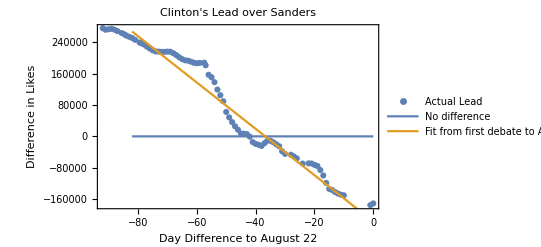

```mathematica
Show[ListPlot[{dayTimes,data[[All,findIndex["Clinton"]]]-data[[All,findIndex["Sanders"]]]}//Transpose,
PlotLegends->{"Actual Lead"}],
Plot[{0,
Normal[LinearModelFit[{dayTimes[[35;;-4]],data[[35;;-4,findIndex["Clinton"]]]-data[[35;;-4,findIndex["Sanders"]]]}//Transpose,{x},x]]/.{x->t}},{t,-Length[data],0},
PlotLegends->{"No difference","Fit from first\ndebate to \nAugust 19"}],
PlotLabel->"Clinton's Lead over Sanders",
FrameLabel->{"Day Difference to August 22","Difference in Likes"},
Frame->True
]
```

```mathematica
LinearModelFit[{dayTimes[[35;;#]]-dayTimes[[35]],data[[35;;#,findIndex["Clinton"]]]-data[[35;;#,findIndex["Sanders"]]]}//Transpose,{x},x]["AdjustedRSquared"]&/@Range[37,Length[data]]
```

{0.970448,0.911148,0.943355,0.971373,0.983417,0.989498,0.985443,0.988817,0.991758,0.992933,0.992074,0.990442,0.982903,0.971353,0.962089,0.959835,0.956401,0.950856,0.944284,0.92974,0.908073,0.886971,0.869972,0.857503,0.848539,0.847702,0.849059,0.846283,0.84498,0.845293,0.84851,0.847261,0.845477,0.844779,0.844688,0.8481,0.854899,0.864416,0.874192,0.882681,0.89031,0.897074,0.902993,0.908043,0.91138,0.912763}

```mathematica
Flatten[Position[(DateObject[#]<gopDebates[[2]])&/@times,False]][[1]]
```

74

```mathematica
(*Some options...

dayToStart=DateObject[times[[1]]];

dayToStart=gopDebates[[1]];
dayToStart=gopDebates[[2]];
*)
dayToStart=times[[Max[firstRecordingDates]]];
dataStart=Flatten[Position[(DateObject[#]≥DateObject[dayToStart])&/@times,True]][[1]];
Manipulate[
Quiet[Quiet[
Labeled[TableForm[Sort[{lastNamesWithParty[[#]],(LinearModelFit[({dayTimes[[dataStart;;]],data[[dataStart;;,#]]}//Transpose),{x},x]["BestFit"]/.{x->time})}&/@(findIndex/@lastNamesWithoutParty),#1[[2]]>#2[[2]]&]],
"Estimated Total Likes from Linear Fit\n"<>DatePlus[times[[Length[times]]],time]
,Top]],{Part::pkspec1}],{time,1,QuantityMagnitude[DateDifference[Today,DateObject[{2050,11,8}]]],1}]
```

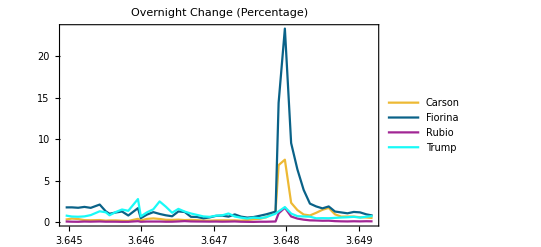

```mathematica
graphFn[3,{findIndex["Carson"],findIndex["Fiorina"],findIndex["Rubio"],findIndex["Trump"]},1,{RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.09955000000000003, 0.9795987, 0.9698177],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[1, 0.998367, 0.434775],RGBColor[0.45412399999999997, 0., 0.441245],RGBColor[0., 0.07322799999999996, 0.848096],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0., 0.0016329999999999956, 0.565225],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0.566842, 0.967407, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.4, 0.8, 1],RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.20956699999999995, 0.549706, 0.]}]
```

```mathematica
CloudDeploy[%294,Permissions->"Public"]
```

CloudObject[]

```mathematica
(*
(* VERY OLD CODE *)
SetDirectory[NotebookDirectory[]];
data2=Import["like_data.csv"];
bin=Databin["66W7CW2x"];
names=data2[[1]];
data2=data2[[2;;]];
InvalidNum=-1;
emptyData=Table[Table[

If[Or[Length[data2[[j]]]<i,
StringLength[ToString[data2[[j,i]]]]==0],
InvalidNum,data2[[j,i]]]

,{i,Length[names]}],{j,Length[data2]}];
data2=emptyData;

(* Add literally everything *)
For[i=1,i≤Length[data2],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[i,1;;Length[names]]]}]]]]
(*  THIS IS THE IMPORTANT ONE -- HOW TO ADD IN CASE OF ERROR   *)
data2=Import["like_data.csv"];
names=data2[[1]];
DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data2[[Length[data2],1;;Length[names]]]}]]]


times=(DateObject/@Dataset[bin][All,"Timestamp"]);*)
(*ResetTheDatabin[]:=For[i=0,i<Length[data],i++,DatabinRemove[bin,1]]*)
(*For[i=1,i≤Length[data],i++,DatabinAdd[bin,Association[MapThread[#1->#2&,{names,data[[i]]}]]]]*)
```

```mathematica
RandomSample[Flatten[{#,ColorNegate[#]}&/@Flatten[MapThread[{#1,#2}&,{(*Table[ColorData["VisibleSpectrum"][410+(i/22)^1*(720-410)],{i,1,21,1}],*)ColorData[60,"ColorList"],ColorData[54,"ColorList"]}]]],22]
```

{RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0., 0.6, 0.6],RGBColor[0.04072600000000004, 0.38550399999999996, 0.533684],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.436362, 0.393744, 0.06414900000000001],RGBColor[0.17006200000000005, 0.27484600000000003, 0.],RGBColor[0.501961, 0, 0.25098],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.09955000000000003, 0.9795987, 0.9698177],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[1, 0.998367, 0.434775],RGBColor[0.45412399999999997, 0., 0.441245],RGBColor[0., 0.07322799999999996, 0.848096],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0., 0.0016329999999999956, 0.565225],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.7268939999999999, 0.45700799999999997, 0.504417],RGBColor[0.566842, 0.967407, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.4, 0.8, 1],RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.20956699999999995, 0.549706, 0.]}

```mathematica
Module[{m},m=Sort[{#,100(data[[Length[data],findIndex[#]]]/data[[firstRecordingDates[[findIndex[#]]],findIndex[#]]]-1)//N,data[[Length[data],findIndex[#]]]}&/@lastNamesWithParty,#1[[2]]>#2[[2]]&];
Labeled[TableForm[{"+"<>ToString[#[[1]]]<>"%",#[[2]]}&/@m[[All,{2,3}]],TableHeadings->{m[[All,1]],{"Percent Change","Total Likes"}}],"Percent change since July 3",Top]]
```

| Percent Change | Total Likes
Fiorina (R) | +383.589% | 473733
Carson (R) | +151.308% | 4100594
Sanders (D) | +125.077% | 1625761
Trump (R) | +93.3608% | 3913215
Clinton (D) | +45.8025% | 1454934
Bush (R) | +34.7369% | 283384
Webb (D) | +30.0234% | 31649
Chafee (D) | +22.781% | 9766
Pataki (R) | +18.011% | 19093
Kasich (R) | +17.8687% | 146433
Cruz (R) | +17.1093% | 1479625
Graham (R) | +15.371% | 136402
Rubio (R) | +15.148% | 1040385
Christie (R) | +14.3961% | 125949
O'Malley (D) | +9.97926% | 80055
Jindal (R) | +9.80156% | 284027
Huckabee (R) | +4.30341% | 1847011
Walker (R) | +3.91585% | 293953
Paul (R) | +1.99481% | 2066828
Biden (D) | +1.71246% | 849893
Santorum (R) | +1.02844% | 265431
Perry (R) | +0.876534% | 1208170Percent change since July 3

```mathematica
(*(* Probably one-time code to fix Scott Walker. I originally copied in the first value recorded, but this made things kinda messy. Instead, I'm going to store -1. *)
newbin=bin;
(* Set "constant placeholders" to -1 *)
linesToUpdate=Flatten[Position[DateObject[#]<DateObject["15 Jul 2015 13:13:00"]&/@times,True]];
data[[linesToUpdate,findIndex["Walker"]]]=InvalidNum;
(* Try adding new rows to a Databin INCLUDING timestamp *)
DatabinAdd[newbin,Association[Join[MapThread[#1->#2&,{names,data[[#]]}],{"Timestamp"->times[[#]]}]]]&/@linesToUpdate;
(* Delete old rows *)
For[i=1,i≤Length[linesToUpdate],i++,DatabinRemove[newbin,Sort[linesToUpdate,Greater][[i]]]]
*)
```

```mathematica
Max[firstRecordingDates]
```

36